```mathematica
β[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=
β[ω,δ,t,ϵ1,ϵ2,m]=ReplacePart[ReplacePart[ReplacePart[0*IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t],Table[{a,a},{a,1,2m,2}]->ω+ⅈ*δ-ϵ1],Table[{b,b},{b,2,2m,2}]->ω+ⅈ*δ-ϵ2]
```

```mathematica
β[ω,δ,t,ϵ1,ϵ2,7]//MatrixForm
```

(ⅈ δ-ϵ1+ω | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -t
-t | ⅈ δ-ϵ2+ω | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -t | ⅈ δ-ϵ1+ω | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -t | 0 | 0
0 | 0 | -t | ⅈ δ-ϵ2+ω | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -t | ⅈ δ-ϵ1+ω | -t | 0 | 0 | 0 | -t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ2+ω | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ1+ω | -t | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ2+ω | -t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ1+ω | -t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -t | 0 | 0 | 0 | -t | ⅈ δ-ϵ2+ω | -t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ1+ω | -t | 0 | 0
0 | 0 | -t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ2+ω | -t | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ1+ω | -t
-t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -t | ⅈ δ-ϵ2+ω)

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=LEFT[ω,δ,t,ϵ1,ϵ2,m]=Module[{J=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],B:=Inverse[β[ω,δ,t,ϵ1,ϵ2,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,25000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Inverse[β[ω,δ,t,ϵ1,ϵ2,m]]
SR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=SR[ω,δ,t,ϵ1,ϵ2,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ1,ϵ2,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ1,ϵ2,m].T1[t,m]].g[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=SR[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].SR[ω,δ,t,ϵ2,ϵ1,m].ConjugateTranspose[ρ[t,m]]].SL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].SL[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]].SR[ω,δ,t,ϵ2,ϵ1,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IL[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IL[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= IR[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[IR[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= SR[ω,δ,t,ϵ2,ϵ1,m].ρ[t,m].IL[ω,δ,t,ϵ1,ϵ2,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:= Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ1,ϵ2,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ1_,ϵ2_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].grr[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m].ρ[t,m].GNON[ω,δ,t,ϵ1,ϵ2,m]]]
```

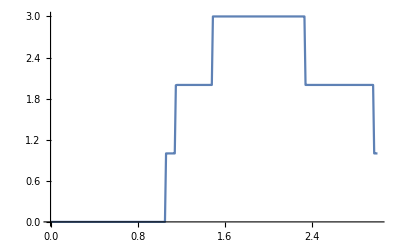

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,-1,1,9]},{ω,Range[0,4,0.01]}]]
```

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,-1,1,11]},{ω,Range[0,4,0.01]}]]
```

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,-1,1,13]},{ω,Range[0,4,0.01]}]]
```

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,-1,1,15]},{ω,Range[0,4,0.01]}]]
```